### Task 1

```mathematica
m=6.39*10^23;
M=4.018*10^30;
G=6.67408*10^-11;
```

### a)

```mathematica
sol=NDSolve[{m*x''[t]==-m*M*G*x[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*y''[t]==-m*M*G*y[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*z''[t]==-m*M*G*z[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),x[0]==10^9,y[0]==0,z[0]==0,x'[0]==0,y'[0]==.9*10^5,z'[0]==0},{x,y,z},{t,0,5000}]
```

{{x→InterpolatingFunction[{{0., 5000.}}, <>],y→InterpolatingFunction[{{0., 5000.}}, <>],z→InterpolatingFunction[{{0., 5000.}}, <>]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,5000},ImageSize->Large]
```

-Graphics3D-

### b)

```mathematica
solb=NDSolve[{m*x''[t]==-m*M*G*x[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*y''[t]==-m*M*G*y[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*z''[t]==-m*M*G*z[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),x[0]==10^9,y[0]==0,z[0]==0,x'[0]==0,y'[0]==.9*10^5,z'[0]==0},{x,y,z},{t,0,500000}]
```

{{x→InterpolatingFunction[{{0., 500000.}}, <>],y→InterpolatingFunction[{{0., 500000.}}, <>],z→InterpolatingFunction[{{0., 500000.}}, <>]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.solb],{t,0,500000},ImageSize->Large]
```

-Graphics3D-

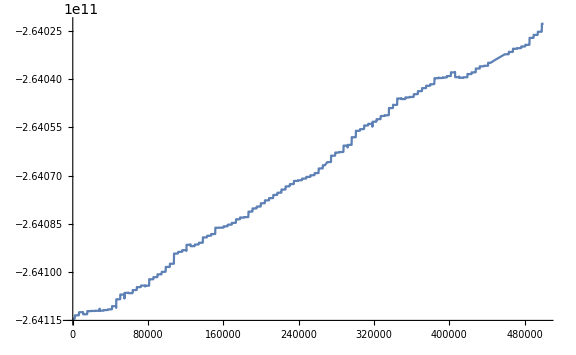

```mathematica
Plot[Evaluate[{(1/2)(x'[t]^2+y'[t]^2+z'[t]^2)-M*G/(√(x[t]^2+y[t]^2+z[t]^2))}/.solb],{t,0,500000},ImageSize->Large]
```

### c)

```mathematica
solc=NDSolve[{m*x''[t]==-m*M*G*x[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*y''[t]==-m*M*G*y[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*z''[t]==-m*M*G*z[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),x[0]==10^8,y[0]==0,z[0]==0,x'[0]==10,y'[0]==10^5,z'[0]==10^5},{x,y,z},{t,0,5000}]
```

{{x→InterpolatingFunction[{{0., 5000.}}, <>],y→InterpolatingFunction[{{0., 5000.}}, <>],z→InterpolatingFunction[{{0., 5000.}}, <>]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.solc],{t,0,5000},ImageSize->Large]
```

-Graphics3D-

### d)

```mathematica
sold=NDSolve[{m*x''[t]==-m*M*G*x[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*y''[t]==-m*M*G*y[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*z''[t]==-m*M*G*z[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),x[0]==10^8,y[0]==0,z[0]==0,x'[0]==10^5,y'[0]==0,z'[0]==0},{x,y,z},{t,0,50}]
```

{{x→InterpolatingFunction[{{0., 50.}}, <>],y→InterpolatingFunction[{{0., 50.}}, <>],z→InterpolatingFunction[{{0., 50.}}, <>]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sold],{t,0,50},BoxRatios->10000,ImageSize->Large]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sold],{t,0,50},BoxRatios->100000,ImageSize->Large]
```

-Graphics3D-

### e)

```mathematica
sole=NDSolve[{m*x''[t]==-m*M*G*x[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*y''[t]==-m*M*G*y[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),m*z''[t]==-m*M*G*z[t]/(x[t]^2+y[t]^2+z[t]^2)^(3/2),x[0]==10^8,y[0]==10^8,z[0]==10,x'[0]==10^8,y'[0]==10^8,z'[0]==100},{x,y,z},{t,0,500}]
```

{{x→InterpolatingFunction[{{0., 500.}}, <>],y→InterpolatingFunction[{{0., 500.}}, <>],z→InterpolatingFunction[{{0., 500.}}, <>]}}

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sole],{t,0,500},BoxRatios->10000,ImageSize->Large]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sole],{t,0,500},BoxRatios->100000,ImageSize->Large]
```

-Graphics3D-

### iii.

### Task 2

### i.

```mathematica
SSE[e_,d_]:=(2.53569*10^8-(e*d)/(1+e*Cos[π/5]))^2+(3.39708*10^8-(e*d)/(1+e*Cos[2π/5]))^2+(5.85633*10^8-(e*d)/(1+e*Cos[3π/5]))^2+(1.41333*10^9-(e*d)/(1+e*Cos[4π/5]))^2+(3.07142*10^9-(e*d)/(1+e*Cos[π]))^2+(1.41332*10^9-(e*d)/(1+e*Cos[6π/5]))^2+(5.8631*10^8-(e*d)/(1+e*Cos[7π/5]))^2+(3.39718*10^8-(e*d)/(1+e*Cos[8π/5]))^2+(2.53566*10^8-(e*d)/(1+e*Cos[9π/5]))^2+(2.31178*10^8-(e*d)/(1+e*Cos[2π]))^2
```

```mathematica
NMinimize[{SSE[e,d],0≤e≤1,0≤d≤ 100000},{e,d}]
```

{5.09107×10^18,{e→0.999967,d→99999.9}}

The gradient of the SSE represents the direction in which the parameters change the most.

### iii.

```mathematica
ans=NDSolve[{theta'[t]==√(G*M*.999967*99999.9)/r^2,theta[0]==0},theta[t],{t,0,20π}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{theta'[t]==(5.17837×10^12)/r^2,theta[0]==0},theta[t],{t,0,20 π}]

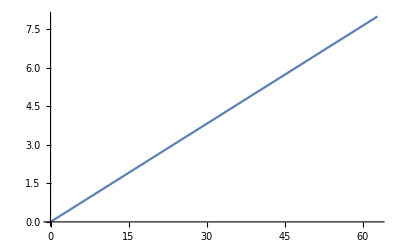

```mathematica
Plot[theta[t]/.ans,{t,0,20π}]
```

### iv.

```mathematica
e=.999967;
d=99999.9;
```

```mathematica
r[t_]=(e*d)/(1+e*Cos[t]);
```

```mathematica
gamma[t_]={r[t],theta[t]/.ans}
Animate[Graphics[{PointSize[Large],Red,Point[{r[theta[t]/.ans]Cos[theta[t]/.ans],r[theta[t]]Sin[theta[t]/.ans]}]},PlotRange->{{-300000000,100000000},{-100000000,100000000}},Axes->True,AxesLabel->{"x","y"}],{t,0,20π}]
```

ReplaceAll::reps: {NDSolve[{theta'[t]==(5.17837×10^12)/r^2,theta[0]==0},theta[t],{t,0,20 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{99996.6/(1+0.999967 Cos[t]),theta[t]/.NDSolve[{theta'[t]==(5.17837×10^12)/r^2,theta[0]==0},theta[t],{t,0,20 π}]}

```mathematica
{99996.6000033/(1+0.999967 Cos[t]),theta[t]/.NDSolve[{theta'[t]==(5.178372493502952*^12)/r^2,theta[0]==0},theta[t],{t,0,20 π}]}
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{theta'[t]==(5.17837×10^12)/r^2,theta[0]==0},theta[t],{t,0,20 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{99996.6/(1+0.999967 Cos[t]),theta[t]/.NDSolve[{theta'[t]==(5.17837×10^12)/r^2,theta[0]==0},theta[t],{t,0,20 π}]}

### Task 3 i.

Vector field is conservative. Can be determined by partial derivative rule. Both are equal to zero. The potential function can be found through the derivation, integration tecnique where you integrate the P function with restect to y, take the derivative to find g’(y), and then setting g’(y) to the Q function to determine the value of g(y). Below is work.
∫-(G m M1)/x^2ⅆy
(-(G m M1 y)/x^2)+g(y)
D[(-(G m M1 y)/x^2),y]
g (y)-(G m M1 y)/x^2
-(G m M1)/x^2+g'(y)=-(G m M2)/(x-x0)
g'(y)=-(G m M2)/(x-x0)^2+(G m M1)/x^2
∫-(G m M2)/(x-x0)+(G m M1)/x^2 ⅆy
Potential function = -(G m M2)/(x-x0)^2

### ii.

```mathematica
M1=1.989*10^30;
M2=4.018*10^30;
m=2000;
G=6.67408*10^-11;
x0={10.1,9.8,8.7};
F1=-((m*M1*G)/x^3)*x
F2=-((m*M2*G)/(x-x0)^3)*(x-x0)
{5.257612673267326*^21,5.584434285714284*^21,7.085864299114811*^21}
VectorPlot3D[{{5.257612673267326*^21,5.584434285714284*^21,7.085864299114811*^21}},{x,10,100},{y,10,100},{z,10,100},VectorScale->Large,VectorStyle->Blue,AxesLabel->{"x","y"}]
```

-(2.65495×10^23)/x^2

{-(5.36329×10^23)/(-10.1+x)^2,-(5.36329×10^23)/(-9.8+x)^2,-(5.36329×10^23)/(-8.7+x)^2}

{5.25761×10^21,5.58443×10^21,7.08586×10^21}

-Graphics3D-

### Task 4

### i.

```mathematica
G=6.67408*10^-11;
M=5.98*10^24;
r=6.38*10^6;
```

```mathematica
Ve=2.23694*√(2(G*M)/r)
```

5.18048×10^10 √(1/r)

### ii.

```mathematica
c=6000;
S=.1;
A=600;
Vf=25019;
```

```mathematica
NMinimize[{M1+M2,25019≤ c*(Log[(M1+M2+A)/(S*M1+M2+A)]+Log[(M2+A)/(S*M2+A)])},{M1,M2}]
```

NMinimize::ivar: 1.989×10^30 is not a valid variable.

NMinimize[{6.007×10^30,False},{1.989×10^30,4.018×10^30}]

Rowan crowley A1 told me I needed to minimize M1+M2, not the parameter. 01MAR17

### iii.

```mathematica
3*∫_(6.371*10^6)^(6.38*10^6) -(M*((799656+212606.2+A)*G*(t/√3))/(3*(t/√3)^2)^(3/2))*(1/√3)ⅆt
```

-8.9507×10^10

This calculation of energy is when the rocket has lost both of its boosters and is just the payload.